## Bayesian Statistics, Assignment for Tuesday, Oct. 29 — SOLUTION

## For Problem Set 10 — There were TWO problem sets numbered Problem Set 10 — OOPS — The other was due Friday, Nov. 1 and has already been returned

### The Author Problem

What is going to be different in this problem vs. Donovan & Mickey’s example?!? I just want you to assume that Federalist Paper 54 had 16 fewer words (but still had 2 occurrences of “upon”). That means that the frequency per thousand words is:

2/1992*1000=1.004

This puts it in a different observation bin!! It is now in the (1, 2] bin. You will see that you get a very different result when you rework the calculation with Paper 54 in the (1, 2] bin. So let’s do it! The explanation of the algebra we need to do is much longer than the actual algebra:

Pr(H|observed frequency is in bin (1,2] )=(Pr(observed frequency is in bin (1,2] |H)*Pr(H))/(Pr(observed frequency is in bin (1,2]|H)*Pr(H)+Pr(observed frequency is in bin (1,2]|~H)*Pr(~H))=(10/48 * 48/98)/(10/48 * 48/98+2/50*50/98)=10/(10+2)=5/6=0.83

Pr(~H|observed frequency is in bin (1,2] )=(Pr(observed frequency is in bin (1,2] |~H)*Pr(~H))/(Pr(observed frequency is in bin (1,2]|H)*Pr(H)+Pr(observed frequency is in bin (1,2]|~H)*Pr(~H))=(2/50 * 50/98)/(10/48 * 48/98+2/50*50/98)=2/(10+2)=1/6=0.17

Let’s make a plot now, like that on p. 57, but with our new results.

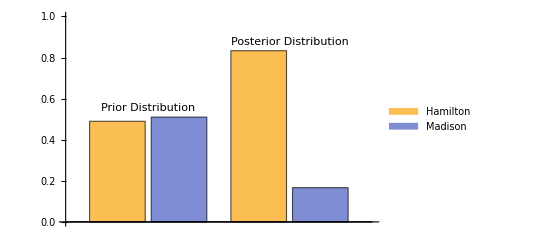

```mathematica
BarChart[{{Legended[48/98, "Hamilton"],Legended[50/98, "Madison"]},{5/6,1/6}},ChartLayout-> "Grouped", PlotRange->{All, {0,1}},
ChartLabels->{Placed[{"Prior Distribution","Posterior Distribution"},Above],Placed[{"",""},Above]}]
```

If having just 16 fewer words changes the result so much, then this whole calculation is fishy.